```mathematica
Predicting Gold Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

## Resources

- PAXG hourly price: Recent (≥ 2020) data - Gemini.

## In This Notebook

LPPLS model implementation (2026 ed.) for Gold price in USD.
Uses PAXG price as a proxy for Gold’s price, due to current lack of access to high quality (hourly) Spot Gold price data.

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-02-04

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Gemini_PAXGUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2020-10-31

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, 0], "ISODate"]==lastPriceDate, lastDownloadedTime=="23:00:00"}
```

{2026-02-04,23:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Convert to seconds *)
hourlyPricesTs={#[[1]]/1000, #[[2]]}&/@closingPricesFilter
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[hourlyPricesTs, First]
```

```mathematica
Length[hourlyPrices]
```

46148

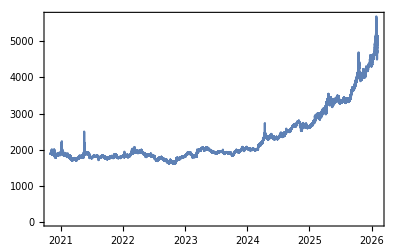

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Gold(PAXG)_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Gold(PAXG)_price-hourly-20201031-20260204.csv

```mathematica
{FromUnixTime[hourlyPrices[[1]][[1]]],FromUnixTime[hourlyPrices[[-1]][[1]]]}
```

{Sat 31 Oct 2020 05:00:00GMT+1,Thu 5 Feb 2026 00:00:00GMT+1}

```mathematica
(* Use the Log Price *)
logPrice= {#[[1]], Log[#[[2]]]}&/@hourlyPrices
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2024-08-01", lastPriceDate}, {"2025-07-01", "2026-01-28"}(* Pre-crash *) }
```

{{2024-08-01,2026-02-04},{2025-07-01,2026-01-28}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1722466800,1770159600},{1751324400,1769554800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{552,211}

```mathematica
bubbles=Table[Select[logPrice,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1722466800,7.79838},{1751324400,8.11043}}

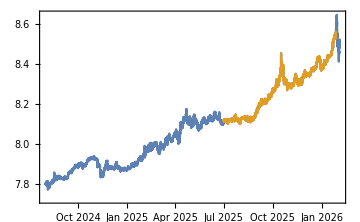

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.01045,0.841281},{1.00059,0.992607}}

```mathematica
Length/@bubblesScaled
```

{13249,5065}

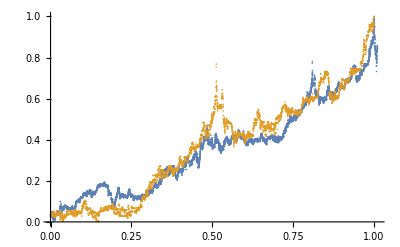

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Gold-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold-1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Gold-2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.5135,13225.9},{17.5819,5041.86}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{5.22814,0.0198828,0.00102353},{2.71495,0.0232076,0.00244685}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

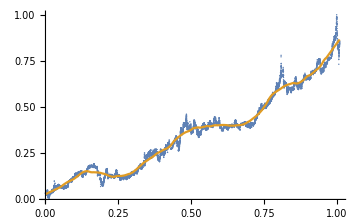
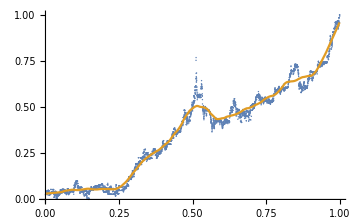

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

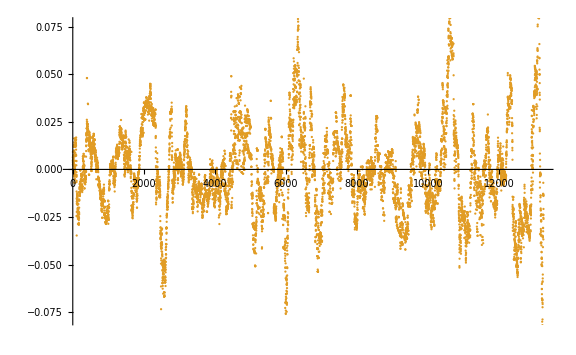
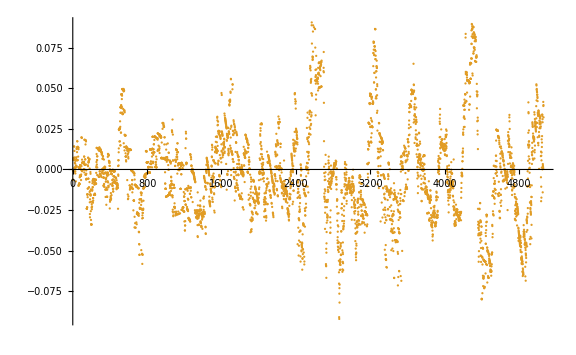

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0237975,0.0300438}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{7.50583,4.5776}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{7.50583 > 5.22814,4.5776 > 2.71495}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0238174,0.0301151}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0238174 > 0.0198828,0.0301151 > 0.0232076}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0198778,0.0231924}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0238224,0.0301317}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0238224 > 0.0198828,0.0301317 > 0.0232076}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.019882,0.0232052}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

1

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.5135,13225.9}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.01045

2.11914

```mathematica
(* Define 7 days resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.0126812

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0181159

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=
Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Thu 5 Feb 2026 09:28:47GMT+1[]

{64668.9,{{a→2.2844,b→-2.07485,c→-0.0437001,d→-0.00725114,T_1→0.,tc→1.32758,m→0.3,ω→14.,RSS→12.014,ℛerror→0.000907268,ℛσ→0.0301141,LL→49863.1,ρ→0.982434,σ→-0.00561938,μ→1.43922×10^-17},{a→3.24612,b→-3.02684,c→-0.0391484,d→-0.0196146,T_1→0.0181159,tc→1.34026,m→0.2,ω→14.,RSS→11.4244,ℛerror→0.000878532,ℛσ→0.0296332,LL→48888.3,ρ→0.981554,σ→-0.00566519,μ→-4.49273×10^-17},{a→1.17031,b→-1.07392,c→0.0282603,d→0.0562972,T_1→0.0362319,tc→1.04859,m→0.4,ω→8.1,RSS→10.8307,ℛerror→0.0008484,ℛσ→0.0291205,LL→47934.5,ρ→0.980671,σ→-0.00569767,μ→-1.01625×10^-17},{a→1.16731,b→-1.0687,c→0.0349848,d→0.0560596,T_1→0.0543478,tc→1.04859,m→0.4,ω→8.2,RSS→10.0322,ℛerror→0.000800718,ℛσ→0.0282902,LL→46946.1,ρ→0.979116,σ→-0.00575121,μ→-1.58002×10^-17},{a→1.16088,b→-1.05776,c→0.0397171,d→0.0578302,T_1→0.0724638,tc→1.04859,m→0.4,ω→8.2,RSS→8.80512,ℛerror→0.000716387,ℛσ→0.0267589,LL→45958.6,ρ→0.976194,σ→-0.00580375,μ→-1.12728×10^-17},{a→1.15795,b→-1.05254,c→0.0467182,d→0.0560263,T_1→0.0905797,tc→1.04859,m→0.4,ω→8.3,RSS→8.07497,ℛerror→0.0006699,ℛσ→0.025876,LL→44977.6,ρ→0.974355,σ→-0.00582232,μ→-1.93575×10^-18},{a→1.15595,b→-1.04911,c→0.0482934,d→0.0561259,T_1→0.108696,tc→1.04859,m→0.4,ω→8.3,RSS→7.93926,ℛerror→0.000671908,ℛσ→0.0259146,LL→43985.3,ρ→0.974074,σ→-0.00586238,μ→-4.57837×10^-18},{a→1.15555,b→-1.04841,c→0.0486125,d→0.0561002,T_1→0.126812,tc→1.04859,m→0.4,ω→8.3,RSS→7.92159,ℛerror→0.000684135,ℛσ→0.0261492,LL→43055.6,ρ→0.974322,σ→-0.00588751,μ→1.53173×10^-17},{a→1.15573,b→-1.04873,c→0.048482,d→0.0561781,T_1→0.144928,tc→1.04859,m→0.4,ω→8.3,RSS→7.88706,ℛerror→0.000695447,ℛσ→0.0263643,LL→42065.9,ρ→0.974231,σ→-0.00594625,μ→2.28988×10^-18},{a→1.16003,b→-1.05628,c→0.0453987,d→0.0576672,T_1→0.163043,tc→1.04859,m→0.4,ω→8.3,RSS→7.44666,ℛerror→0.000670628,ℛσ→0.0258895,LL→41089.4,ρ→0.972665,σ→-0.00601157,μ→3.68266×10^-17},{a→1.16454,b→-1.06453,c→0.0376736,d→0.0626698,T_1→0.181159,tc→1.04859,m→0.4,ω→8.2,RSS→6.83392,ℛerror→0.000628927,ℛσ→0.0250715,LL→40129.7,ρ→0.970477,σ→-0.00604685,μ→1.65223×10^-17},{a→1.16356,b→-1.06278,c→0.0381766,d→0.0620569,T_1→0.199275,tc→1.04859,m→0.4,ω→8.2,RSS→6.6757,ℛerror→0.000628065,ℛσ→0.0250542,LL→39209.4,ρ→0.970194,σ→-0.00607108,μ→2.43767×10^-18},{a→1.16496,b→-1.06529,c→0.0375401,d→0.0629879,T_1→0.217391,tc→1.04859,m→0.4,ω→8.2,RSS→6.5379,ℛerror→0.000629189,ℛσ→0.0250764,LL→38240.3,ρ→0.969768,σ→-0.00611911,μ→-4.04817×10^-17},{a→1.019,b→-0.948581,c→0.0134291,d→0.0768041,T_1→0.235507,tc→1.03591,m→0.5,ω→7.5,RSS→6.42808,ℛerror→0.000633059,ℛσ→0.0251532,LL→37265.3,ρ→0.969302,σ→-0.00618415,μ→-2.97295×10^-17},{a→1.02332,b→-0.958108,c→0.0051055,d→0.0813106,T_1→0.253623,tc→1.03591,m→0.5,ω→7.4,RSS→6.16117,ℛerror→0.000621336,ℛσ→0.0249191,LL→36296.,ρ→0.968094,σ→-0.00624406,μ→5.80473×10^-18},{a→1.02393,b→-0.959437,c→0.00491126,d→0.0820407,T_1→0.271739,tc→1.03591,m→0.5,ω→7.4,RSS→6.13939,ℛerror→0.0006343,ℛσ→0.0251775,LL→35333.3,ρ→0.968144,σ→-0.00630393,μ→-1.04899×10^-17},{a→1.02345,b→-0.958392,c→0.00493133,d→0.081449,T_1→0.289855,tc→1.03591,m→0.5,ω→7.4,RSS→6.12671,ℛerror→0.000648947,ℛσ→0.0254664,LL→34359.5,ρ→0.968141,σ→-0.00637657,μ→2.06226×10^-17},{a→1.02285,b→-0.957046,c→0.00483561,d→0.0806949,T_1→0.307971,tc→1.03591,m→0.5,ω→7.4,RSS→6.10885,ℛerror→0.000663717,ℛσ→0.0257543,LL→33411.2,ρ→0.968279,σ→-0.00643495,μ→3.20634×10^-18},{a→1.02277,b→-0.956869,c→0.0048342,d→0.0805899,T_1→0.326087,tc→1.03591,m→0.5,ω→7.4,RSS→6.09476,ℛerror→0.000679763,ℛσ→0.0260636,LL→32472.7,ρ→0.968509,σ→-0.00648894,μ→2.96785×10^-17},{a→1.02314,b→-0.957719,c→0.00510593,d→0.080985,T_1→0.344203,tc→1.03591,m→0.5,ω→7.4,RSS→6.04996,ℛerror→0.000693087,ℛσ→0.0263175,LL→31618.8,ρ→0.969138,σ→-0.00648742,μ→6.58806×10^-18},{a→1.02537,b→-0.962894,c→0.0155579,d→0.0832473,T_1→0.362319,tc→1.03591,m→0.5,ω→7.5,RSS→5.74341,ℛerror→0.000676412,ℛσ→0.0259987,LL→30874.8,ρ→0.969115,σ→-0.00641112,μ→-1.75056×10^-17},{a→1.02883,b→-0.970973,c→0.0191969,d→0.0859051,T_1→0.380435,tc→1.03591,m→0.5,ω→7.5,RSS→5.48841,ℛerror→0.000664939,ℛσ→0.025777,LL→30058.2,ρ→0.968978,σ→-0.00637035,μ→-9.72251×10^-18},{a→0.958103,b→-0.940329,c→0.0093401,d→0.102582,T_1→0.398551,tc→1.03591,m→0.6,ω→7.4,RSS→5.39948,ℛerror→0.000673588,ℛσ→0.0259439,LL→29250.5,ρ→0.969926,σ→-0.0063143,μ→-1.81316×10^-17},{a→1.02712,b→-0.966888,c→0.016996,d→0.0853322,T_1→0.416667,tc→1.03591,m→0.5,ω→7.5,RSS→5.33178,ℛerror→0.000685407,ℛσ→0.0261702,LL→28389.,ρ→0.970432,σ→-0.00631638,μ→-1.69189×10^-17},{a→1.02641,b→-0.965155,c→0.016044,d→0.0854332,T_1→0.434783,tc→1.03591,m→0.5,ω→7.5,RSS→5.27456,ℛerror→0.000699451,ℛσ→0.0264366,LL→27513.4,ρ→0.970901,σ→-0.00633068,μ→1.0435×10^-18},{a→1.02463,b→-0.960678,c→0.00448678,d→0.0864042,T_1→0.452899,tc→1.03591,m→0.5,ω→7.4,RSS→5.21457,ℛerror→0.000713933,ℛσ→0.0267086,LL→26620.3,ρ→0.971296,σ→-0.00635284,μ→8.22521×10^-18},{a→1.02059,b→-0.950534,c→-0.00986378,d→0.086995,T_1→0.471014,tc→1.03591,m→0.5,ω→7.3,RSS→4.82956,ℛerror→0.000683492,ℛσ→0.0261326,LL→25928.7,ρ→0.971529,σ→-0.00619091,μ→-9.977×10^-18},{a→1.06124,b→-1.00995,c→0.0587249,d→0.0600596,T_1→0.48913,tc→1.04859,m→0.5,ω→8.3,RSS→4.36127,ℛerror→0.000638639,ℛσ→0.0252602,LL→25255.9,ρ→0.971096,σ→-0.0060289,μ→-3.93566×10^-18},{a→0.991557,b→-0.992175,c→0.0798572,d→0.0553712,T_1→0.507246,tc→1.04859,m→0.6,ω→8.4,RSS→4.22275,ℛerror→0.000640684,ℛσ→0.0253002,LL→24429.8,ρ→0.971794,σ→-0.00596617,μ→2.71638×10^-17}}}

```mathematica
(* Shortcut: *)
    fits=
```

```mathematica
(* Timing in hours: *)
fits[[1]]/60/60
```

17.9636

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.32758 | ℛσ→0.0301141 | LL→49863.1
T_1→0.0181159 | tc→1.34026 | ℛσ→0.0296332 | LL→48888.3
T_1→0.0362319 | tc→1.04859 | ℛσ→0.0291205 | LL→47934.5
T_1→0.0543478 | tc→1.04859 | ℛσ→0.0282902 | LL→46946.1
T_1→0.0724638 | tc→1.04859 | ℛσ→0.0267589 | LL→45958.6
T_1→0.0905797 | tc→1.04859 | ℛσ→0.025876 | LL→44977.6
T_1→0.108696 | tc→1.04859 | ℛσ→0.0259146 | LL→43985.3
T_1→0.126812 | tc→1.04859 | ℛσ→0.0261492 | LL→43055.6
T_1→0.144928 | tc→1.04859 | ℛσ→0.0263643 | LL→42065.9
T_1→0.163043 | tc→1.04859 | ℛσ→0.0258895 | LL→41089.4
T_1→0.181159 | tc→1.04859 | ℛσ→0.0250715 | LL→40129.7
T_1→0.199275 | tc→1.04859 | ℛσ→0.0250542 | LL→39209.4
T_1→0.217391 | tc→1.04859 | ℛσ→0.0250764 | LL→38240.3
T_1→0.235507 | tc→1.03591 | ℛσ→0.0251532 | LL→37265.3
T_1→0.253623 | tc→1.03591 | ℛσ→0.0249191 | LL→36296.
T_1→0.271739 | tc→1.03591 | ℛσ→0.0251775 | LL→35333.3
T_1→0.289855 | tc→1.03591 | ℛσ→0.0254664 | LL→34359.5
T_1→0.307971 | tc→1.03591 | ℛσ→0.0257543 | LL→33411.2
T_1→0.326087 | tc→1.03591 | ℛσ→0.0260636 | LL→32472.7
T_1→0.344203 | tc→1.03591 | ℛσ→0.0263175 | LL→31618.8
T_1→0.362319 | tc→1.03591 | ℛσ→0.0259987 | LL→30874.8
T_1→0.380435 | tc→1.03591 | ℛσ→0.025777 | LL→30058.2
T_1→0.398551 | tc→1.03591 | ℛσ→0.0259439 | LL→29250.5
T_1→0.416667 | tc→1.03591 | ℛσ→0.0261702 | LL→28389.
T_1→0.434783 | tc→1.03591 | ℛσ→0.0264366 | LL→27513.4
T_1→0.452899 | tc→1.03591 | ℛσ→0.0267086 | LL→26620.3
T_1→0.471014 | tc→1.03591 | ℛσ→0.0261326 | LL→25928.7
T_1→0.48913 | tc→1.04859 | ℛσ→0.0252602 | LL→25255.9
T_1→0.507246 | tc→1.04859 | ℛσ→0.0253002 | LL→24429.8

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.06215

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.03591

1.34026

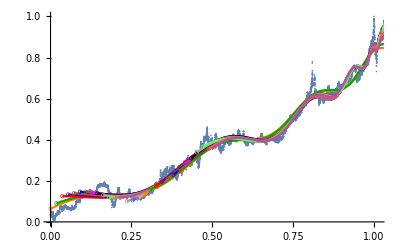

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0181159,0.0362319,0.0543478,0.0724638,0.0905797,0.108696,0.126812,0.144928,0.163043,0.181159,0.199275,0.217391,0.235507,0.253623,0.271739,0.289855,0.307971,0.326087,0.344203,0.362319,0.380435,0.398551,0.416667,0.434783,0.452899,0.471014,0.48913,0.507246}

{0.000907268,0.000878532,0.0008484,0.000800718,0.000716387,0.0006699,0.000671908,0.000684135,0.000695447,0.000670628,0.000628927,0.000628065,0.000629189,0.000633059,0.000621336,0.0006343,0.000648947,0.000663717,0.000679763,0.000693087,0.000676412,0.000664939,0.000673588,0.000685407,0.000699451,0.000713933,0.000683492,0.000638639,0.000640684}

{12.014,11.4244,10.8307,10.0322,8.80512,8.07497,7.93926,7.92159,7.88706,7.44666,6.83392,6.6757,6.5379,6.42808,6.16117,6.13939,6.12671,6.10885,6.09476,6.04996,5.74341,5.48841,5.39948,5.33178,5.27456,5.21457,4.82956,4.36127,4.22275}

{0.0301141,0.0296332,0.0291205,0.0282902,0.0267589,0.025876,0.0259146,0.0261492,0.0263643,0.0258895,0.0250715,0.0250542,0.0250764,0.0251532,0.0249191,0.0251775,0.0254664,0.0257543,0.0260636,0.0263175,0.0259987,0.025777,0.0259439,0.0261702,0.0264366,0.0267086,0.0261326,0.0252602,0.0253002}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

13249

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

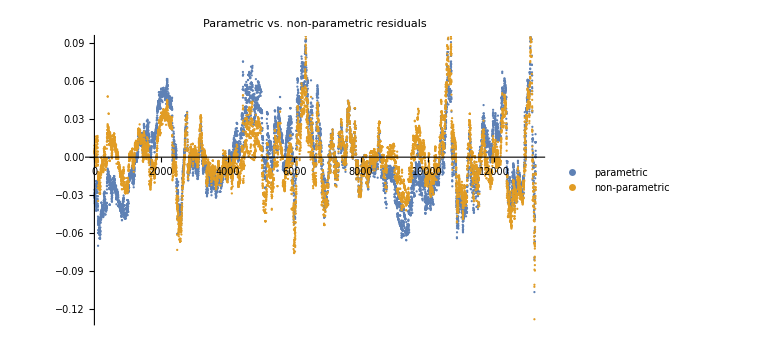

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{7.50583,12.014}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0238224,0.0301209}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.000567508,0.000907268}

```mathematica
selN=Length[T1s];
selN
```

29

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{13249,13009,12769,12529,12289,12049,11809,11569,11329,11089,10849,10609,10369,10129,9889,9649,9409,9169,8929,8689,8449,8209,7969,7729,7489,7249,7009,6769,6529}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{13249,13009,12769,12529,12289,12049,11809,11569,11329,11089,10849,10609,10369,10129,9889,9649,9409,9169,8929,8689,8449,8209,7969,7729,7489,7249,7009,6769,6529}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-Gold-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{13249,13009,12769,12529,12289,12049,11809,11569,11329,11089,10849,10609,10369,10129,9889,9649,9409,9169,8929,8689,8449,8209,7969,7729,7489,7249,7009,6769,6529}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.000907268,0.000878532,0.0008484,0.000800718,0.000716387,0.0006699,0.000671908,0.000684135,0.000695447,0.000670628,0.000628927,0.000628065,0.000629189,0.000633059,0.000621336,0.0006343,0.000648947,0.000663717,0.000679763,0.000693087,0.000676412,0.000664939,0.000673588,0.000685407,0.000699451,0.000713933,0.000683492,0.000638639,0.000640684}

```mathematica
RSSs
```

{12.014,11.4244,10.8307,10.0322,8.80512,8.07497,7.93926,7.92159,7.88706,7.44666,6.83392,6.6757,6.5379,6.42808,6.16117,6.13939,6.12671,6.10885,6.09476,6.04996,5.74341,5.48841,5.39948,5.33178,5.27456,5.21457,4.82956,4.36127,4.22275}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0237975,0.0239413,0.024094,0.0242829,0.0243977,0.024583,0.0247482,0.0249596,0.0251694,0.0250194,0.0249502,0.0244525,0.0245944,0.0248721,0.0250692,0.0253146,0.0255373,0.0258297,0.0261214,0.0263498,0.0264125,0.0266116,0.0266638,0.0269092,0.0271812,0.0272964,0.0270009,0.0261797,0.0263531}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.971888,σ→-0.0056028,μ→-0.0000138298},{ρ→0.971872,σ→-0.00563822,μ→-0.0000109036},{ρ→0.971936,σ→-0.00566778,μ→-0.0000145347},{ρ→0.971922,σ→-0.0057136,μ→-0.0000189211},{ρ→0.971673,σ→-0.00576564,μ→-0.0000102878},{ρ→0.971642,σ→-0.00581262,μ→-6.72732×10^-6},{ρ→0.971492,σ→-0.00586683,μ→-0.0000143623},{ρ→0.971716,σ→-0.00589407,μ→-0.0000162438},{ρ→0.971656,σ→-0.00594981,μ→-0.0000138985},{ρ→0.970732,σ→-0.00600855,μ→-0.000033691},{ρ→0.970179,σ→-0.0060474,μ→-0.0000488667},{ρ→0.968605,σ→-0.00607874,μ→-0.000025677},{ρ→0.96846,σ→-0.00612787,μ→-0.0000278423},{ρ→0.96851,σ→-0.00619225,μ→-0.0000298156},{ρ→0.968355,σ→-0.00625634,μ→-0.0000371521},{ρ→0.968344,σ→-0.00631874,μ→-0.0000289322},{ρ→0.968168,σ→-0.00639169,μ→-0.0000185218},{ρ→0.968285,σ→-0.00645321,μ→-0.0000130909},{ρ→0.968631,σ→-0.00649085,μ→-7.43995×10^-6},{ρ→0.969252,σ→-0.00648357,μ→-6.66347×10^-6},{ρ→0.970211,σ→-0.00639836,μ→-0.0000241635},{ρ→0.970961,σ→-0.00636608,μ→-0.000036424},{ρ→0.9713,σ→-0.00634182,μ→-0.0000186489},{ρ→0.972324,σ→-0.00628662,μ→-0.0000135463},{ρ→0.97232,σ→-0.00635057,μ→-0.0000120083},{ρ→0.972777,σ→-0.00632536,μ→-1.43933×10^-6},{ρ→0.973397,σ→-0.00618613,μ→-5.2747×10^-6},{ρ→0.973013,σ→-0.00604051,μ→-0.0000424507},{ρ→0.97408,σ→-0.00596068,μ→-0.000047259}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[-0.0000138298,{0.971888},0.0000313913],ARProcess[-0.0000109036,{0.971872},0.0000317895],ARProcess[-0.0000145347,{0.971936},0.0000321238],ARProcess[-0.0000189211,{0.971922},0.0000326452],ARProcess[-0.0000102878,{0.971673},0.0000332427],ARProcess[-6.72732×10^-6,{0.971642},0.0000337866],ARProcess[-0.0000143623,{0.971492},0.0000344197],ARProcess[-0.0000162438,{0.971716},0.0000347401],ARProcess[-0.0000138985,{0.971656},0.0000354003],ARProcess[-0.000033691,{0.970732},0.0000361027],ARProcess[-0.0000488667,{0.970179},0.0000365711],ARProcess[-0.000025677,{0.968605},0.000036951],ARProcess[-0.0000278423,{0.96846},0.0000375508],ARProcess[-0.0000298156,{0.96851},0.0000383439],ARProcess[-0.0000371521,{0.968355},0.0000391418],ARProcess[-0.0000289322,{0.968344},0.0000399264],ARProcess[-0.0000185218,{0.968168},0.0000408537],ARProcess[-0.0000130909,{0.968285},0.0000416439],ARProcess[-7.43995×10^-6,{0.968631},0.0000421311],ARProcess[-6.66347×10^-6,{0.969252},0.0000420367],ARProcess[-0.0000241635,{0.970211},0.000040939],ARProcess[-0.000036424,{0.970961},0.0000405269],ARProcess[-0.0000186489,{0.9713},0.0000402187],ARProcess[-0.0000135463,{0.972324},0.0000395217],ARProcess[-0.0000120083,{0.97232},0.0000403297],ARProcess[-1.43933×10^-6,{0.972777},0.0000400101],ARProcess[-5.2747×10^-6,{0.973397},0.0000382682],ARProcess[-0.0000424507,{0.973013},0.0000364877],ARProcess[-0.000047259,{0.97408},0.0000355297]}

{49898.5,48912.6,47946.3,46941.9,45937.3,44936.,43933.3,42991.2,41992.7,41003.6,40030.7,39101.8,38122.7,37134.4,36157.1,35180.9,34199.2,33238.,32320.,31466.9,30705.,29870.2,29028.2,28225.2,27268.8,26474.2,25721.2,24987.6,24194.7}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

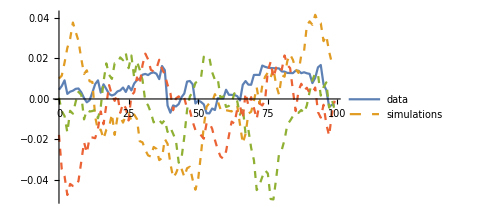
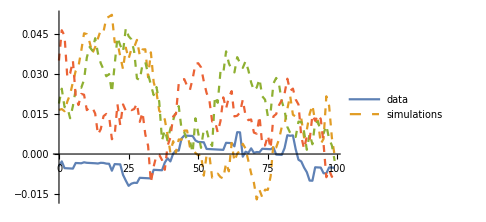
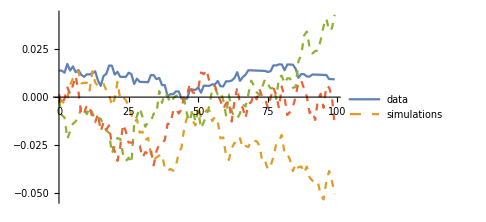
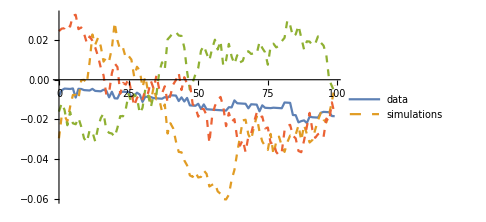
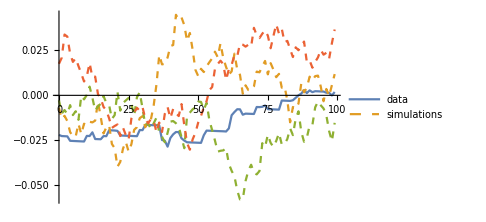
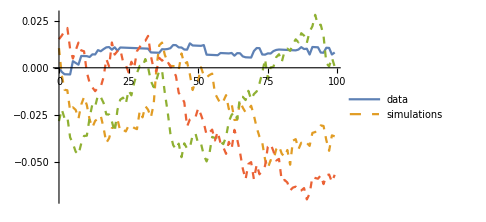
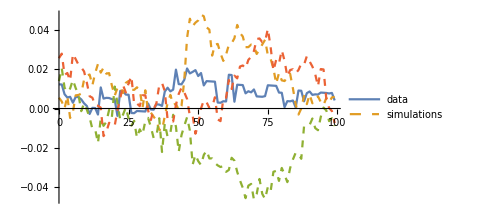
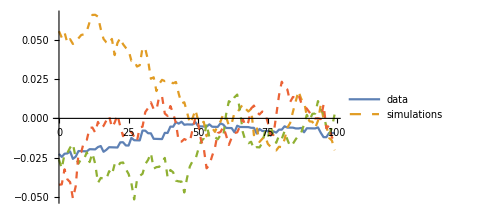

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.5135,13225.9},{17.52,12985.9},{17.5254,12745.9},{17.5324,12505.9},{17.5077,12266.},{17.5146,12025.9},{17.5214,11785.9},{17.5277,11545.9},{17.5351,11305.9},{17.5082,11066.},{17.5155,10825.9},{17.5234,10585.9},{17.5302,10345.9},{17.5389,10105.9},{17.5084,9865.95},{17.517,9625.94},{17.5256,9385.93},{17.5337,9145.92},{17.5432,8905.9},{17.509,8665.95},{17.5184,8425.94},{17.5288,8185.92},{17.5377,7945.91},{17.5494,7705.9},{17.5094,7465.95},{17.5208,7225.93},{17.5325,6985.92},{17.5437,6745.9},{17.5571,6505.89}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

13225.9

17.5135

{13225.9,12985.9,12745.9,12505.9,12266.,12025.9,11785.9,11545.9,11305.9,11066.,10825.9,10585.9,10345.9,10105.9,9865.95,9625.94,9385.93,9145.92,8905.9,8665.95,8425.94,8185.92,7945.91,7705.9,7465.95,7225.93,6985.92,6745.9,6505.89}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 29.8594 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 29.8595 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 4524022 Kb

Memory Used: 25.5452 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,9,86,120,110,123,187,457,258,318,394,569,578,523,528,522,487,645,777,738,729,692,656,757,768,788}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.009,0.086,0.12,0.11,0.123,0.187,0.457,0.258,0.318,0.394,0.569,0.578,0.523,0.528,0.522,0.487,0.645,0.777,0.738,0.729,0.692,0.656,0.757,0.768,0.788}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

6

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

5

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.03591

14

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

6

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.15795,b→-1.05254,c→0.0467182,d→0.0560263,T_1→0.0905797,tc→1.04859,m→0.4,ω→8.3,RSS→8.07497,ℛerror→0.0006699,ℛσ→0.025876,LL→44977.6,ρ→0.974355,σ→-0.00582232,μ→-1.93575×10^-18,index→6}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

6

{a→1.15795,b→-1.05254,c→0.0467182,d→0.0560263,T_1→0.0905797,tc→1.04859,m→0.4,ω→8.3,RSS→8.07497,ℛerror→0.0006699,ℛσ→0.025876,LL→44977.6,ρ→0.974355,σ→-0.00582232,μ→-1.93575×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.4

8.3

1.04859

44977.6

```mathematica
t1=Subscript[T, 1]/.fit
```

0.0905797

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

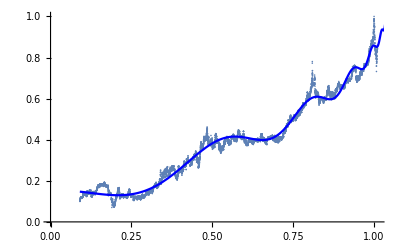

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.15795,b→-1.05254,c→0.0467182,d→0.0560263,T_1→0.0905797,tc→1.04859,m→0.4,ω→8.3,RSS→8.07497,ℛerror→0.0006699,ℛσ→0.025876,LL→44977.6,ρ→0.974355,σ→-0.00582232,μ→-1.93575×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.974355,σ→-0.00582232,μ→-2.16616×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92006

{1.04586,1.04859}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92002

{1.04586,1.04859,1.05136}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.01045

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Mon 23 Feb 2026 08:16:47

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Tue 24 Feb 2026 20:05:56

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Thu 26 Feb 2026 08:21:23

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Wed 4 Mar 2026 05:49:41

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Mon 3 Aug 2026 04:08:26

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Tue 17 Feb 2026 21:50:11

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Thu 1 Aug 2024 00:00:00 | tc→1.32758 | Mon 27 Jul 2026 05:52:41
T_1→0.0181159 | Sat 10 Aug 2024 21:31:05 | tc→1.34026 | Mon 3 Aug 2026 04:08:26
T_1→0.0362319 | Tue 20 Aug 2024 19:02:10 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.0543478 | Fri 30 Aug 2024 16:33:15 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.0724638 | Mon 9 Sep 2024 14:04:20 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.0905797 | Thu 19 Sep 2024 11:35:26 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.108696 | Sun 29 Sep 2024 09:06:31 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.126812 | Wed 9 Oct 2024 06:37:36 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.144928 | Sat 19 Oct 2024 04:08:41 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.163043 | Tue 29 Oct 2024 01:39:46 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.181159 | Thu 7 Nov 2024 23:10:52 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.199275 | Sun 17 Nov 2024 20:41:57 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.217391 | Wed 27 Nov 2024 18:13:02 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.235507 | Sat 7 Dec 2024 15:44:07 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.253623 | Tue 17 Dec 2024 13:15:13 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.271739 | Fri 27 Dec 2024 10:46:18 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.289855 | Mon 6 Jan 2025 08:17:23 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.307971 | Thu 16 Jan 2025 05:48:28 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.326087 | Sun 26 Jan 2025 03:19:33 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.344203 | Wed 5 Feb 2025 00:50:39 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.362319 | Fri 14 Feb 2025 22:21:44 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.380435 | Mon 24 Feb 2025 19:52:49 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.398551 | Thu 6 Mar 2025 17:23:54 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.416667 | Sun 16 Mar 2025 14:55:00 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.434783 | Wed 26 Mar 2025 12:26:05 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.452899 | Sat 5 Apr 2025 09:57:10 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.471014 | Tue 15 Apr 2025 07:28:15 | tc→1.03591 | Tue 17 Feb 2026 21:50:11
T_1→0.48913 | Fri 25 Apr 2025 04:59:20 | tc→1.04859 | Tue 24 Feb 2026 20:05:56
T_1→0.507246 | Mon 5 May 2025 02:30:26 | tc→1.04859 | Tue 24 Feb 2026 20:05:56

```mathematica
(* Compute price at the low leg of the best Tc: *)
bestP=bestLppls[bestTc-epsilon,bestTc]
```

1.13088

```mathematica
lowCIP=bestLppls[lowCItc,bestTc]
```

1.06502

```mathematica
lastScaledP=bubbleBest[[-1]][[2]]
```

0.841281

```mathematica
lastPriceDate
```

2026-02-04

```mathematica
(* Closing price at `lastPriceDate` date: *)
latestPrice=hourlyPrices[[-1]][[2]]
```

5054.66

```mathematica
(* Plot predicted price evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVP[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestPrice/Exp[lastScaledP]]]},{i,min, max,1/8}]
```

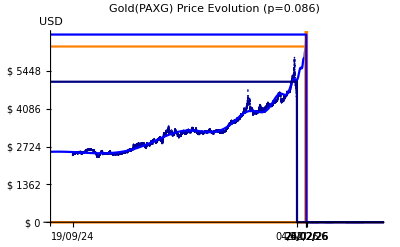

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"Gold(PAXG) Price Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,Exp[bestP]}}, Ticks->{ticksH,ticksVP},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestP+1],UnitStep[ti-highCItc]Exp[bestP+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIP],UnitStep[bestTc-ti]Exp[bestP],UnitStep[lastScaledTc-ti]Exp[lastScaledP]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/Gold(PAXG)_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/Gold(PAXG)_PricePrediction-2026-02-04.png

```mathematica
pToPrice[p_]:= Exp[p] latestPrice/Exp[lastScaledP]
```

```mathematica
(* Check: *)
lastPrice=pToPrice[lastScaledP]
```

5054.66

```mathematica
lowCIPrice=pToPrice[lowCIP]
```

6322.1

```mathematica
bestPrice=pToPrice[bestP]
```

6752.47